```mathematica
Quit[];
```

```mathematica
$LoadAddOns = {"FeynArts","FeynHelpers"};
<< FeynCalc`
$FAVerbose = 0;
```

FeynCalc 10.0.0 (stable version). For help, use the online documentation, visit the forum and have a look at the supplied examples.

If you use FeynCalc in your research, please evaluate FeynCalcHowToCite[] to learn how to cite this software.

Please keep in mind that the proper academic attribution of our work is crucial to ensure the future development of this package!

FeynArts 3.11 (25 Mar 2022) patched for use with FeynCalc, for documentation see the manual or visit www.feynarts.de.

If you use FeynArts in your research, please cite

• T. Hahn, Comput. Phys. Commun., 140, 418-431, 2001, arXiv:hep-ph/0012260

FeynHelpers 1.3.0, for more information see the accompanying publication.

Have a look at the supplied examples. If you use FeynHelpers in your research, please cite

• V. Shtabovenko, "FeynHelpers: Connecting FeynCalc to FIRE and Package-X", Comput. Phys. Commun., 218, 48-65, 2017, arXiv:1611.06793

Furthermore, remember to cite the authors of the tools that you are calling from FeynHelpers, which are

• FIRE by A. Smirnov, if you are using the function FIREBurn.

• Package-X by H. Patel, if you are using the function PaXEvaluate.

```mathematica
FAPatch[PatchModelsOnly->True,FAModelsDirectory->FileNameJoin[{NotebookDirectory[],"QED_Broad_Resonance_FA"}]]
```

Successfully patched FeynArts.

```mathematica
Diags=DiagramExtract[InsertFields[CreateTopologies[0, 2 -> 3, ExcludeTopologies->{Tadpoles,WFCorrections}],{F[2,{1}],-F[2,{1}]}->{V[1],F[2,{2}],-F[2,{2}]}, InsertionLevel->{Classes},Model -> FileNameJoin[{NotebookDirectory[],"QED_Broad_Resonance_FA", "QED_Broad_Resonance_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"QED_Broad_Resonance_FA", "QED_Broad_Resonance_FA"}]],{5,7}];
Amp=FCFAConvert[CreateFeynAmp[Diags,PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{r,k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,FinalSubstitutions->M$FACouplings];
Diags1=InsertFields[CreateTopologies[0, 2 -> 2, ExcludeTopologies->{Tadpoles,WFCorrections}],{F[2,{1}],-F[2,{1}]}->{V[1],S[1]}, InsertionLevel->{Classes},Model -> FileNameJoin[{NotebookDirectory[],"QED_Broad_Resonance_FA", "QED_Broad_Resonance_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"QED_Broad_Resonance_FA", "QED_Broad_Resonance_FA"}]];
Amp1=FCFAConvert[CreateFeynAmp[Diags1,PreFactor->1],IncomingMomenta->{p1,p2},OutgoingMomenta->{r,k},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,FinalSubstitutions->M$FACouplings];
Diags2=InsertFields[CreateTopologies[0, 1 -> 2, ExcludeTopologies->{Tadpoles,WFCorrections}],{S[1]}->{F[2,{2}],-F[2,{2}]}, InsertionLevel->{Classes},Model -> FileNameJoin[{NotebookDirectory[],"QED_Broad_Resonance_FA", "QED_Broad_Resonance_FA"}], GenericModel -> FileNameJoin[{NotebookDirectory[],"QED_Broad_Resonance_FA", "QED_Broad_Resonance_FA"}]];
Amp2=FCFAConvert[CreateFeynAmp[Diags2,PreFactor->1],IncomingMomenta->{k},OutgoingMomenta->{k1,k2},UndoChiralSplittings->True,ChangeDimension->4,List->False,SMP->True,Contract->True,FinalSubstitutions->M$FACouplings];
```

```mathematica
FCClearScalarProducts[];
ScalarProduct[k1,k1]=ScalarProduct[k2,k2]=ScalarProduct[r,r]=0;
ScalarProduct[p1,p1]=ScalarProduct[p2,p2]=SMP["m_e"]^2;
ScalarProduct[k1,k2]=minv^2/2;
ScalarProduct[k,k]=minv^2;
ScalarProduct[p1,p2]=(s-2 SMP["m_e"]^2)/2;
ScalarProduct[p1,r]=(s-minv^2)/4+((s-minv^2)√(s-4 SMP["m_e"]^2))/(4 √s)Cos[θ];
ScalarProduct[p2,r]=(s-minv^2)/4-((s-minv^2)√(s-4 SMP["m_e"]^2))/(4 √s)Cos[θ];
ScalarProduct[p1,k]=(s+minv^2)/4-((s-minv^2)√(s-4 SMP["m_e"]^2))/(4 √s)Cos[θ];
ScalarProduct[p2,k]=(s+minv^2)/4+((s-minv^2)√(s-4 SMP["m_e"]^2))/(4 √s)Cos[θ];
ScalarProduct[r,k]=(s-minv^2)/2;
```

```mathematica
AmpSq0=((Amp ComplexConjugate[Amp])//FeynAmpDenominatorExplicit//DoPolarizationSums[#,r,0]&//FermionSpinSum[#,ExtraFactor->1/2^2]&//ReplaceAll[#,{SMP["m_mu"]->0}]&//DiracSimplify//Simplify)/.{Momentum[k2]->Momentum[k]-Momentum[k1]}//ExpandScalarProduct//Simplify;
AmpSq1=(Amp1 ComplexConjugate[Amp1])//FeynAmpDenominatorExplicit//DoPolarizationSums[#,r,0]&//FermionSpinSum[#,ExtraFactor->1/2^2]&//ReplaceAll[#,{SMP["m_mu"]->0}]&//DiracSimplify//Simplify;
AmpSq11=((Numerator[AmpSq1]/.{SMP["m_e"]->0})/Denominator[AmpSq1])//Simplify;
AmpSq2=(Amp2 ComplexConjugate[Amp2])//FeynAmpDenominatorExplicit//ReplaceAll[#,{SMP["m_mu"]->0}]&//FermionSpinSum[#]&//DiracSimplify//Simplify;
```

```mathematica
minvPreDist=(minv(s-minv^2))/(128 π^3 s^2)Integrate[Sin[θ]AmpSq1 AmpSq2,{θ,0,π},Assumptions->{SMP["m_e"]>0,s>4 SMP["m_e"]^2}];
```

```mathematica
minvPreDist
```

(EE^2 minv^3 yl^4 (s-minv^2) (-2 minv^2 √(s (s-4 m_e^2))+2 (-4 m_e^2 (minv^2+2 s)+16 m_e^4+minv^4+s^2) tanh^-1(√(1-(4 m_e^2)/s))+8 m_e^2 √(s (s-4 m_e^2))))/(16 π^3 s (minv^2-s)^2 √(s (s-4 m_e^2)))

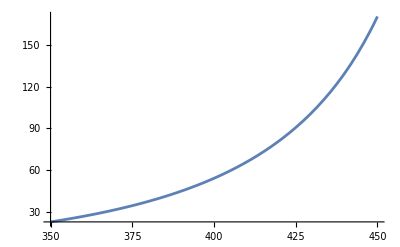

```mathematica
Plot[minvPreDist/.{EE->1,yl->1,SMP["m_e"]->5.1×10^-4,s->500^2},{minv,350,450},PlotRange->All]
```

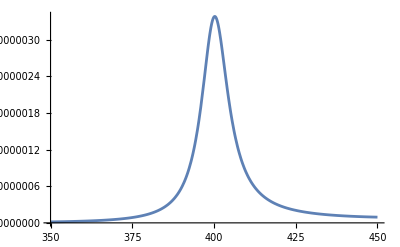

```mathematica
Plot[1/((minv^2-400^2)^2+(400×10)^2)minvPreDist/.{EE->1,yl->1,SMP["m_e"]->5.1×10^-4,s->500^2},{minv,350,450},PlotRange->All]
```

```mathematica
NWATotalCross=π/(2 M^2 Γ)×minvPreDist/.{minv->M};
NWATotalCross/.{EE->1,yl->1,SMP["m_e"]->5.1×10^-4,s->500^2,M->400}
```

0.000529303/Γ

```mathematica
NWATotalCross1=(EE^2 M yl^4(s-M^2)(-2 M^2 s+2(M^4+s^2)ArcTanh[√(1-(4 SMP["m_e"]^2)/s)]))/(32 π^2 Γ s^2(M^2-s)^2);
NWATotalCross2=NWATotalCross1/.{EE->1,yl->1,SMP["m_e"]->5.1×10^-4,s->500^2,M->400,Γ->10}
```

0.0000529303

```mathematica
NIntegrate[1/((minv^2-400^2)^2+(400×10)^2)minvPreDist/.{EE->1,yl->1,SMP["m_e"]->5.1×10^-4,s->500^2},{minv,200,470}]
```

0.0000532776